# GPU Computation for the Masses

Abdul Dakkak

## Purpose

### Cannot assume a user has a GPU/development environment

or a C compiler for that matter. These people should be able to participate

Most of use do not have a C compiler or CUDA on most of our machines, but we still might want to use them to program

### Constraint 1: Support a bazillion users

Should be able to scale from a few users

```mathematica
user=-Graphics-;
server=-Graphics-;
StarGraph[4,VertexShape->{user,1->server},VertexSize->{1->0.5,0.3},EdgeStyle->Directive[Gray,Thick]]
```

-Graphics-

to thousands

```mathematica
user=-Graphics-;
server=-Graphics-;
StarGraph[20,VertexShape->{user,1->server},VertexSize->{1->1,0.3},EdgeStyle->Directive[Gray,Thick]]
```

-Graphics-

### Constraint 2: Support to have a dynamic number of worker nodes

the server is supposed to support one daemon (slave worker)

```mathematica
dae=-Graphics-;
server=-Graphics-;
StarGraph[2,VertexShape->{dae,1->server},VertexSize->{1->0.5,0.3},EdgeStyle->Directive[Gray,Thick]]
```

-Graphics-

or thousands

```mathematica
dae=-Graphics-;
server=-Graphics-;
StarGraph[20,VertexShape->{dae,1->server},VertexSize->{1->1,0.3},EdgeStyle->Directive[Gray,Thick]]
```

-Graphics-

### Architecture

### Constraint 3: Supposed to be user friendly

The course is about learning how to program CUDA, not about how to login to a system and use ssh

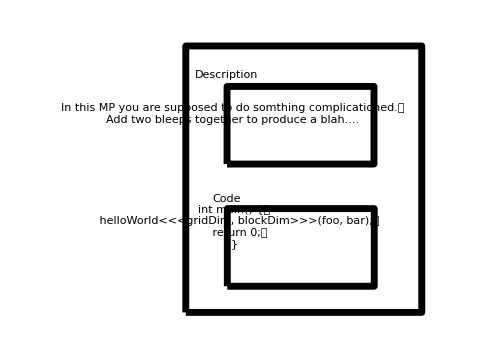
```mathematica
xkcdStyle={FontFamily->"Comic Sans MS",16};

xkcdLabel[{str_,{x1_,y1_},{xo_,yo_}}]:=Module[{x2,y2},x2=x1+xo;y2=y1+yo;
{Inset[Style[str,xkcdStyle],{x2,y2},{1.2 Sign[x1-x2],Sign[y1-y2] Boole[x1==x2]}],Thick,BezierCurve[{{0.9 x1+0.1 x2,0.9 y1+0.1 y2},{x1,y2},{x2,y2}}]}];

xkcdRules={EdgeForm[ef:Except[None]]:>EdgeForm[Flatten@{ef,Thick,Black}],Style[x_,st_]:>Style[x,xkcdStyle],Pane[s_String]:>Pane[Style[s,xkcdStyle]],{h_Hue,l_Line}:>{Thickness[0.02],White,l,Thick,h,l},Grid[{{g_Graphics,s_String}}]:>Grid[{{g,Style[s,xkcdStyle]}}],Rule[PlotLabel,lab_]:>Rule[PlotLabel,Style[lab,xkcdStyle]]};

xkcdShow[p_]:=Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle]/.xkcdRules

xkcdShow[Labeled[p_,rest__]]:=Labeled[Show[p,AxesStyle->Thick,LabelStyle->xkcdStyle],rest]/.xkcdRules

xkcdDistort[p_]:=Module[{r,ix,iy},r=ImagePad[Rasterize@p,30,Padding->White];
{ix,iy}=Table[RandomImage[{-1,1},ImageDimensions@r]~ImageConvolve~GaussianMatrix[10],{2}];
ImagePad[ImageTransformation[r,#+15 {ImageValue[ix,#],ImageValue[iy,#]}&,DataRange->Full],-5]];

xkcdConvert[x_]:=xkcdDistort[xkcdShow[x]]
x=-Graphics-;
xkcdConvert[x]
```

-Graphics-

Users worry about writing their code, nothing else.

### Constraint 4: Supposed to be low risk for deployers

A person should not comprimise the system or interfear with others’ code.

## Demo

## Technical Details

A collection of buzz words

```mathematica
buzz={
cuda=-Graphics-,
node=-Graphics-,
backbone=-Graphics-,
coffee=-Graphics-,
mongodb=-Graphics-,
sandbox=-Graphics-,
bootstrap=-Graphics-
};
StarGraph[Length[buzz],VertexShape->MapThread[#1->#2&,{Range[Length[buzz]],buzz}],VertexSize->0.5,EdgeStyle->Dashed]
```

-Graphics-

### Bootstrap

Provides use with cross platform CSS and Javascript GUI elements for the website’s frontend

### Backbone.js

Provides use with a way to have MVC on the client side

### CUDA

What we are teaching!!!!

### NodeJS

Both the server and worker daemon are written in Node and CoffeeScript

### CoffeeScript

Coffeescript is a language that compiles to Javascript

### Mongodb (will be switched with mysql)

A NoSQL database (will be switched with a SQL database)

### Sandbox

We use a combination of syscall captures and program analysis to make sure nothing malicious is being compiled/executed

## Features

### Login system

### Grading system

### Decentralized

### Sandboxed

### Cross Platform (even on windows)

### Dynamic scheduler

## Demo

```mathematica
e[img_,res_]:=Module[{file=FileNameJoin[{"C:\\Users\\abduld\\Dropbox\\wbGPU\\description\\images",ToString[res]<>".png"}]},Export[file,ImageResize[img,Scaled[0.5]]]]
```

```mathematica
e[-Graphics-,"mp1"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\mp1.png

```mathematica
e[-Graphics-,"mp1_code"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\mp1_code.png

```mathematica
-Graphics--Graphics-
```

## Demo Senarios

### Solution is correct

```mathematica
e[-Graphics-,"correct"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\correct.png

### Solution is incorrect

```mathematica
e[-Graphics-,"incorrect"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\incorrect.png

### Logging and debugging

```mathematica
e[-Graphics-,"logging"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\logging.png

### Timing

```mathematica
e[-Graphics-,"timing"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\timing.png

### Invalid Synax

```mathematica
e[-Graphics-,"syntax"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\syntax.png

### Infinite loop in host code

```mathematica
e[-Graphics-,"timeout"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\timeout.png

### Infinite loop in GPU code

### Allocating too much memory in host code

```mathematica
e[-Graphics-,"memory"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\memory.png

### Restrict user from adding includes

```mathematica
e[-Graphics-,"sandbox_include"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\sandbox_include.png

### Restricted syscall in host code

uses a combination of textual filtering and seccomp (linux kernel syscall filtering)

```mathematica
e[-Graphics-,"sandbox"]
```

C:\Users\abduld\Dropbox\wbGPU\description\images\sandbox.png

### See previous attempts

## Applications

### Teaching GPU Programming

### Remote GPU evaluation from non-accelerated devices

### Batch processing of GPU jobs

## Code Breakdown

### ~5kLOC for C support code (timer/logger/solution verifier/…)

### ~1.5kLOC of coffeescript for the daemon

### ~1.5kLOC of coffeescript for the server

### ~1kLOC of javascript for the interface

## Extending

### Model for running native code in restricted environment

## Questions/Discussion